```mathematica
g=NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,1},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
With[{vertices=VertexList[g]},Table[HighlightGraph[g,Style[PathGraph[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],DirectedEdges->True],Red]],{i,1,Length[vertices]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}


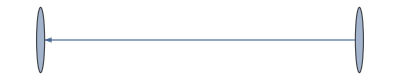
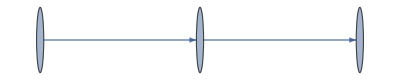
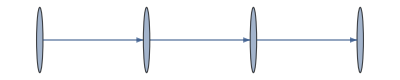
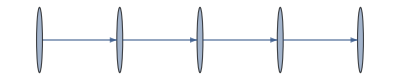
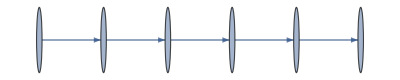
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{vertices=VertexList[g]},Table[Style[PathGraph[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],DirectedEdges->True],Red],{i,1,Length[vertices]}]]
```

```mathematica
FindShortestPath[g,First[VertexList[g]],Last[VertexList[g]]]
```

{{1,1},{0,1},{1,1,0},{1,0,1},{1,1,1,0},{1,0,0,1}}

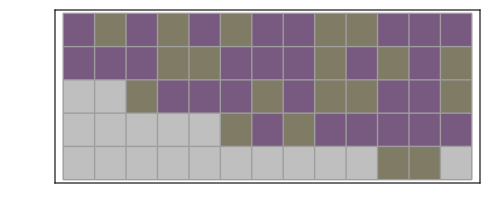

```mathematica
ArrayPlot[Transpose[PadRight[VertexList[-Graphics-],{Automatic,Automatic},0.25]],Frame->True,ColorRules->{0->Hue[0.14,.21,.5],1->Hue[0.8,0.3,0.5]},Mesh->True]
```

```mathematica
Manipulate[GraphPlot[{n->e},DirectedEdges->True],{n,10,25,1},{e,25,50,1}]
```

```mathematica
evcol=Black;EventHandler[Dynamic[Graphics[{evcol,Disk[]},ImageSize->Tiny]],{"MouseClicked":>(evcol=RandomColor[])}]
```

-Graphics-

{{1,1},{0,1},{1,1,0},{0,0,1},{1,0,1},{0,1,1,0},{1,1,0,1},{1,1,1,0},{0,0,0,1},{0,1,0,1},{1,0,1,1,0},{1,1,1,1,0},{1,0,0,1}}

{{1,1}->{0,1},{0,1}->{1,1,0},{1,1,0}->{0,0,1},{1,1,0}->{1,0,1},{0,0,1}->{0,1,1,0},{0,0,1}->{1,1,0,1},{1,0,1}->{1,0,1},{1,0,1}->{1,1,1,0},{0,1,1,0}->{0,0,0,1},{0,1,1,0}->{0,1,0,1},{0,1,1,0}->{1,0,1,1,0},{1,1,0,1}->{0,1,0,1},{1,1,0,1}->{1,1,0,1},{1,1,0,1}->{1,1,1,1,0},{1,1,1,0}->{1,0,0,1},{1,1,1,0}->{1,1,0,1}}

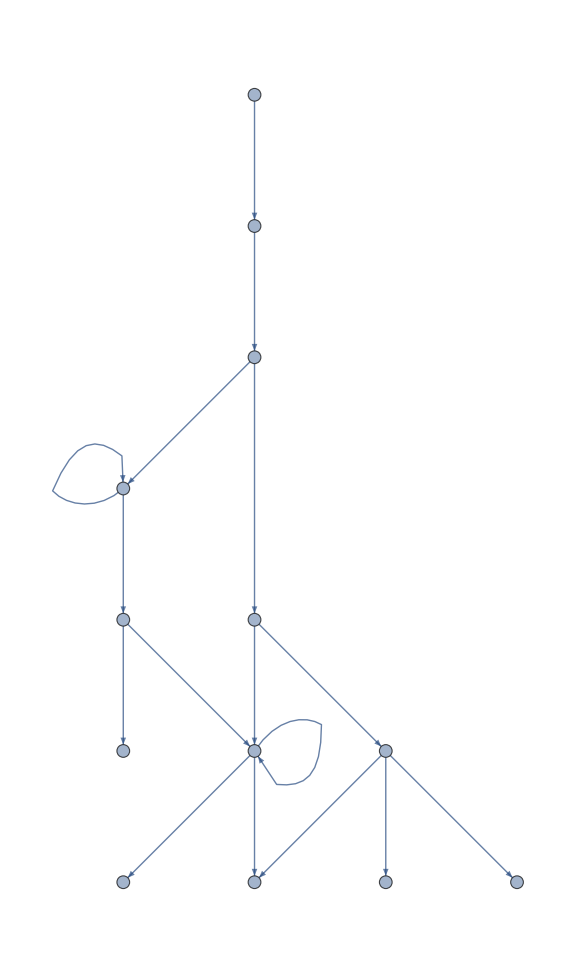

```mathematica
graph = NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,1},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},5,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality",VertexLabels->Automatic]
VertexList[graph]
EdgeList[graph]
Graph[VertexList[graph],EdgeList[graph],ImageSize->Large]
```